```mathematica
SetDirectory[NotebookDirectory[]];
```

### Test BR_aa=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst.dat"];
data[[1]]
```

{1000.,9.999999999999999988×10^-15,0.,0.752507899999957264,0.0000183792399999989577,0.,7.75538032999956623×10^-6,0.06185800999999648,8.10474899999979646×10^-15,4.08745259999976775×10^-10,0.,0.,0.752573399999957204,0.0000179224799999989787,0.,7.83537462999956215×10^-6,0.0618417999999964843,2.6269949999998786×10^-14,4.37593159999975133×10^-10,0.,0.,0.752442499999957271,0.0000188398199999989295,0.,7.68602713999957009×10^-6,0.0618741799999964828,1.26003800000016864×10^-15,3.82641399999978251×10^-10,0.}

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
plotDataDoverH=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data],Map[DoverHhigh,data],Map[DoverHlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

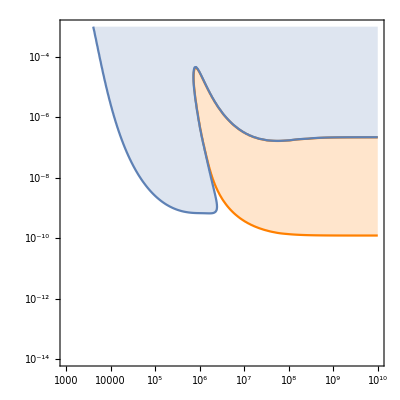

```mathematica
ListContourPlot[plotDataDoverH,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange];
ListContourPlot[plotDataDoverH,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger];
Show[plt1,plt2]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

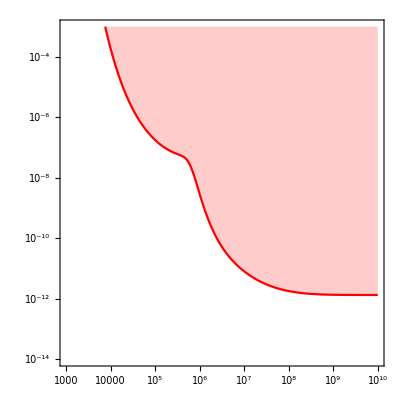

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

```mathematica
He4mean[data_]:=4*data[[8]];
He4high[data_]:=4*data[[17]];
He4low[data_]:=4*data[[26]];
He4obs=2.45*10^-1;
He4err=0.01*10^-1;
deltaHe4[mean_,high_,low_]:=(mean-He4obs)/Sqrt[sigmaTh[mean,high,low]^2+He4err^2];
plotDataHe4=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe4,Map[He4mean,data],Map[He4high,data],Map[He4low,data]]]];
```

General::munfl: 0.-1.97626258336498618×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.+1.97626258336498618×10^-323 is too small to represent as a normalized machine number; precision may be lost.

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

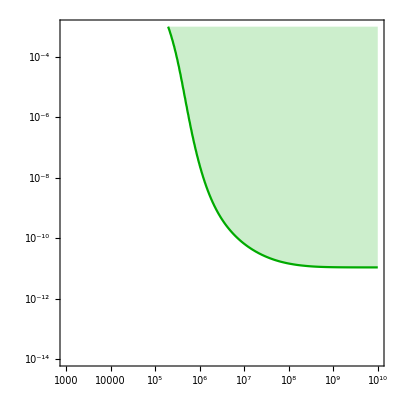

```mathematica
ListContourPlot[plotDataHe4,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt4=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Darker[Green]]
```

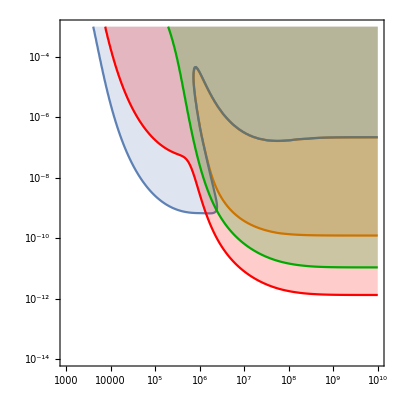

```mathematica
Show[plt1,plt2,plt3,plt4]
```

### Test BR_ee=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst_ee.dat"];
data[[1]]
```

$Aborted

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

data⟦1⟧

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
```

```mathematica
dataDoverHmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,5]]/data[[i,4]]]},{i,1,Length[data]}];
dataHe3overDmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,7]]/data[[i,5]]]},{i,1,Length[data]}];
dataDoverHhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,14]]/data[[i,13]]]},{i,1,Length[data]}];
dataHe3overDhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,16]]/data[[i,14]]]},{i,1,Length[data]}];dataDoverHlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,23]]/data[[i,22]]]},{i,1,Length[data]}];
dataHe3overDlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,25]]/data[[i,23]]]},{i,1,Length[data]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
dataHe3overDlow[[20000;;20020]]
```

{{1.492462311557788868,-2.99999999999999999,1.73614129918733221},{1.507537688442210945,-14.000000000000000001,-0.389374803622645004},{1.507537688442210945,-13.94472361809045145,-0.389374798609256442},{1.507537688442210945,-13.88944723618090471,-0.389374793803672847},{1.507537688442210945,-13.83417085427135617,-0.389374788195775617},{1.507537688442210945,-13.77889447236180942,-0.389374782190557976},{1.507537688442210945,-13.72361809045226088,-0.389374774374201784},{1.507537688442210945,-13.6683417085427141,-0.389374766364638177},{1.507537688442210945,-13.61306532663316561,-0.38937475715308054},{1.507537688442210945,-13.55778894472361883,-0.38937474633563254},{1.507537688442210945,-13.50251256281407028,-0.389374734520943318},{1.507537688442210945,-13.447236180904521743,-0.389374720699743977},{1.507537688442210945,-13.391959798994974989,-0.389374705076972253},{1.507537688442210945,-13.336683417085426455,-0.389374687249801321},{1.507537688442210945,-13.281407035175879727,-0.389374667019508128},{1.507537688442210945,-13.226130653266331167,-0.38937464459067929},{1.507537688442210945,-13.170854271356784442,-0.389374618551724693},{1.507537688442210945,-13.11557788944723588,-0.38937458850252747},{1.507537688442210945,-13.060301507537689154,-0.389374554851835903},{1.507537688442210945,-13.005025125628140619,-0.389374517200357168},{1.507537688442210945,-12.94974874371859388,-0.38937447413870929}}

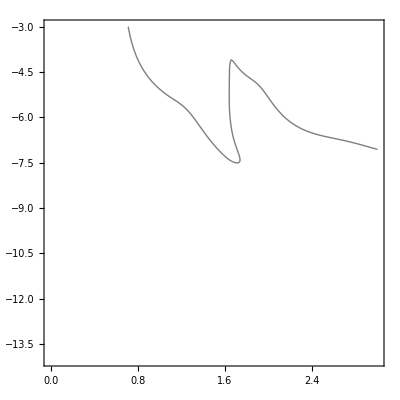

```mathematica
ListContourPlot[dataDoverHhigh,Contours->{-5},ContourShading->Log10[DoverHobs+2*DoverHerr]]
```

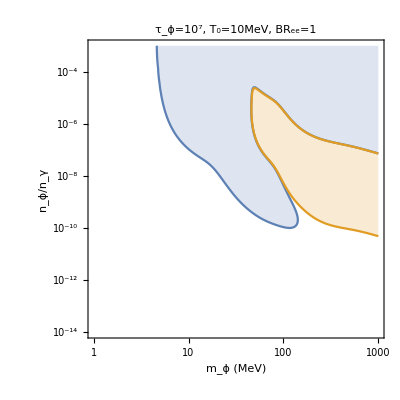

```mathematica
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
ListContourPlot[dataDoverHhigh,Contours->{Log10[DoverHobs+2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
ListContourPlot[dataDoverHlow,Contours->{Log10[DoverHobs-2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%,%%%%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"m_ϕ (MeV)","n_ϕ/n_γ"},PlotLabel->"τ_ϕ=10^7, T_0=10MeV, BR_ee=1"]
```

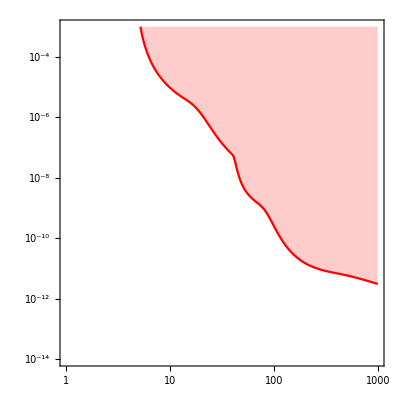

```mathematica
He3overDobs=0.83;
He3overDerr=0.15;
ListContourPlot[dataHe3overDhigh,Contours->{Log10[He3overDobs+2*He3overDerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

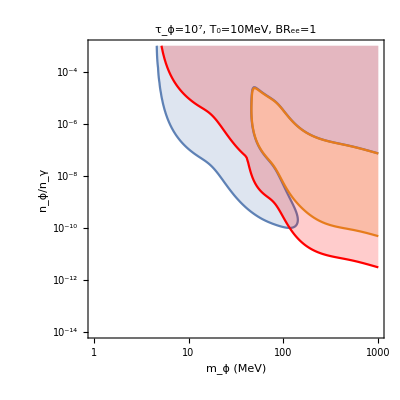

```mathematica
Show[plt1,plt2]
```

### Our Model

```mathematica
Quit[]
```

```mathematica
importData={Import["~/prj/acropolis/MD1_100_MD2_105_MZp_300.dat"],Import["~/prj/acropolis/MD1_100_MD2_110_MZp_300.dat"],Import["~/prj/acropolis/MD1_100_MD2_120_MZp_300.dat"],Import["~/prj/acropolis/MD1_100_MD2_130_MZp_300.dat"]};
importData[[;;,1]]
```

{{-4.,-5.,0.,0.,0.,0.752507898598344771,0.752573398598222809,0.75244249859846668,0.0000183792399657659992,0.0000179224799666167767,0.0000188398199649080994,0.,0.,0.,7.75538031555615014×10^-6,7.83537461540709537×10^-6,7.68602712568538752×10^-6,0.0618580098847804766,0.061841799884810672,0.0618741798847503577,8.1047489849037282×10^-15,2.62699499510684072×10^-14,1.26003799765299644×10^-15,4.08745259238652613×10^-10,4.3759315918491923×10^-10,3.82641399287274834×10^-10,0.,0.,0.},{-4.,-5.,0.,0.,0.,0.75250963205863497,0.752575089012511356,0.752444275464764445,0.0000175131890979594588,0.0000170779521611662059,0.0000179520660322053691,0.,0.,0.,7.75539565411958412×10^-6,7.83539108674137791×10^-6,7.68604144342321436×10^-6,0.0618580100119359017,0.061841800013071685,0.0618741800109123413,8.10855614809201138×10^-15,2.62738855181635309×10^-14,1.26364689078768402×10^-15,3.9320874091974502×10^-10,4.20921799268756917×10^-10,3.68127505591210179×10^-10,0.,0.,0.},{-4.,-5.,0.,0.,0.,0.752516481493869738,0.752581768238117177,0.752451296533594438,0.0000140888717469335401,0.0000137387436379909744,0.0000144419283905844117,0.,0.,0.,7.75519932587278092×10^-6,7.83519617423456191×10^-6,7.68584375395597066×10^-6,0.0618580100717924936,0.061841800077017374,0.0618741800670813344,1.30185811918162047×10^-14,3.15389369753920893×10^-14,5.85004871679951864×10^-15,3.36835326507621355×10^-10,3.60458029373994031×10^-10,3.1544292322456652×10^-10,0.,0.,0.},{-4.,-5.,0.,0.,0.,0.752507911032997967,0.752573410758802575,0.752442511309486473,0.000018373723432428632,0.0000179171005302672211,0.0000188341651880209695,0.,0.,0.,7.7553805116672405×10^-6,7.83537482571150516×10^-6,7.68602730902209109×10^-6,0.0618580100001780084,0.0618418000001921819,0.0618741800001652714,8.1049365943178374×10^-15,2.62701511260583722×10^-14,1.26021332091933832×10^-15,4.0855318154334971×10^-10,4.37386920706675242×10^-10,3.82462068033326042×10^-10,0.,0.,0.}}

```mathematica
data=Table[Block[{data=importData[[k]]},Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}]],{k,1,Length[importData]}];
```

```mathematica
Dimensions[data]
For[i=1,i<Length[data]+1,i++,Print[Dimensions[data[[i]]]]]
```

{4}

{15,29}

{10,29}

{3,29}

{1,29}

```mathematica
(*data=importData[[2]];
data=Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}];
Dimensions[data]*)
```

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
```

```mathematica
plotDataDoverH=Table[Transpose[AppendTo[Transpose[data[[k]]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data[[k]]],Map[DoverHhigh,data[[k]]],Map[DoverHlow,data[[k]]]]]],{k,1,Length[importData]}];
```

Set::setps: Transpose[data⟦k⟧] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

```mathematica
Dimensions[plotDataDoverH]
plotDataDoverH[[1]]
plotDataDoverH[[2]]
plotDataDoverH[[3]]
plotDataDoverH[[4]]
```

{4}

{{-4.,-5.,-1.48908},{-4.,-4.5,-1.48908},{-4.,-4.,-1.49082},{-4.,-3.5,-1.49583},{-4.,-3.,-1.48914},{-3.5,-5.,-1.48908},{-3.5,-4.5,-1.48932},{-3.5,-4.,-1.49},{-3.5,-3.5,-1.48908},{-3.,-5.,-1.48911},{-3.,-4.5,-1.48922},{-3.,-4.,-1.48908},{-2.5,-5.,-1.4891},{-2.5,-4.5,-1.48908},{-2.,-5.,-1.48908}}

{{-4.,-5.,-3.24166},{-4.,-4.5,-9.24684},{-4.,-4.,-1.94664},{-4.,-3.5,-1.48908},{-3.5,-5.,-2.39555},{-3.5,-4.5,-1.57247},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4973},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}

{{-4.,-5.,-11.5643},{-4.,-4.5,-1.49668},{-3.5,-5.,-1.48946}}

{{-4.,-5.,-1.49985}}

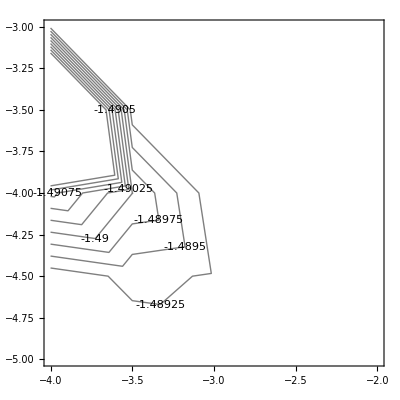

```mathematica
ListContourPlot[plotDataDoverH[[1]],ContourShading->None,ContourLabels->All]
```

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

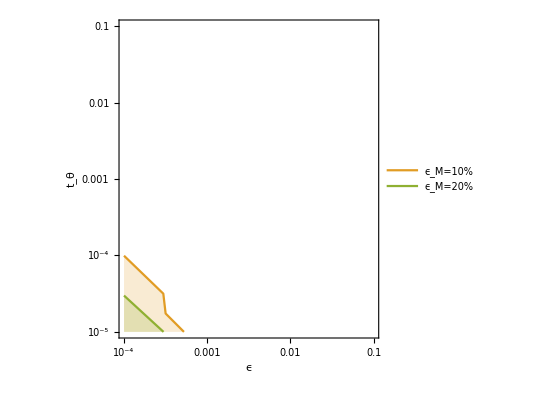

acropolis_bounds_MD1_100_MZp_300.png

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig1=Map[ToLinearScale,%];
(*plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]*)
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig2=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverH[[3]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig3=Map[ToLinearScale,%];
(*Show[ListLogLogPlot[{fig1},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}],ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]]*)
ListLogLogPlot[{fig2,fig3},Joined->True,Filling->Bottom,PlotStyle->{colors[[2]],colors[[3]]},PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"},PlotLegends->{"ϵ_M=10%","ϵ_M=20%"}]
Export["acropolis_bounds_MD1_100_MZp_300.png",%]
```

```mathematica
fig1
```

{10^({}⟦1⟧),10^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

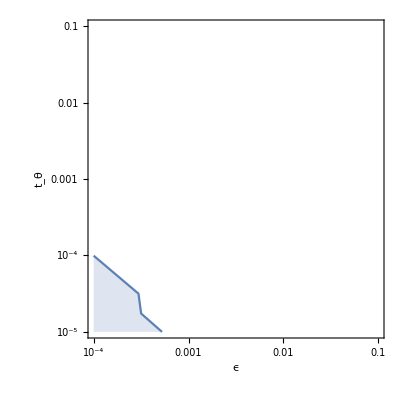

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Set::setps: Transpose[data] in the part assignment is not a symbol.

```mathematica
plotDataHe3overD
```

{{-4.,-5.,-2.66844},{-4.,-4.5,-2.55095},{-4.,-4.,-2.699},{-4.,-3.5,-2.70847},{-3.5,-5.,-2.68607},{-3.5,-4.5,-2.70714},{-3.5,-4.,-2.70847},{-3.,-5.,-2.70829},{-3.,-4.5,-2.70847},{-2.5,-5.,-2.70847}}

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red,FrameLabel->{"ϵ","t_θ"}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

```mathematica
He4mean[data_]:=4*data[[8]];
He4high[data_]:=4*data[[17]];
He4low[data_]:=4*data[[26]];
He4obs=2.45*10^-1;
He4err=0.03*10^-1;
deltaHe4[mean_,high_,low_]:=(mean-He4obs)/Sqrt[sigmaTh[mean,high,low]^2+He4err^2];
plotDataHe4=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe4,Map[He4mean,data],Map[He4high,data],Map[He4low,data]]]];
```

Set::setps: Transpose[data] in the part assignment is not a symbol.

```mathematica
plotDataHe4
```

{{-4.,-5.,0.810492},{-4.,-4.5,0.810492},{-4.,-4.,0.810492},{-4.,-3.5,0.810492},{-3.5,-5.,0.810492},{-3.5,-4.5,0.810492},{-3.5,-4.,0.810492},{-3.,-5.,0.810492},{-3.,-4.5,0.810492},{-2.5,-5.,0.810492}}

```mathematica
ListContourPlot[plotDataHe4,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt4=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Darker[Green]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

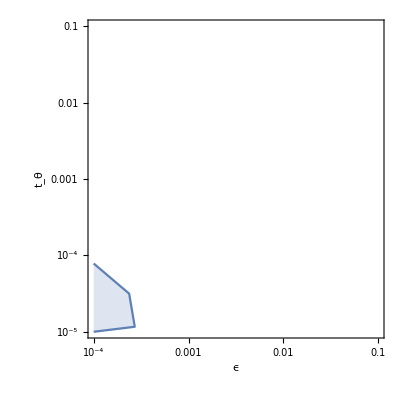

```mathematica
Show[plt1,plt2,plt3,plt4]
```

### Test by comparing with monochromatic source term

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst_1.dat"];
```

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
plotDataDoverH=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data],Map[DoverHhigh,data],Map[DoverHlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogLogPlot::lpn: {10.^({}⟦1⟧),10.^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot[{10^({}⟦1⟧),10^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧,Joined→True,Filling→Top,PlotRange→{{1/10000000000,1/10000},{1/1000000000000,1/1000}},Frame→True,AspectRatio→1,LabelStyle→Larger,FrameLabel→{ϵ,n_ϕ/n_γ},PlotLabel→D/H upper limit,PlotStyle→RGBColor[1, 0.5, 0]]

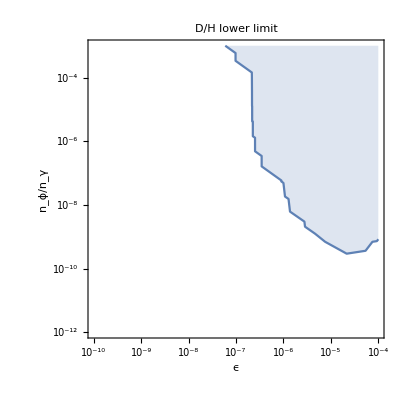

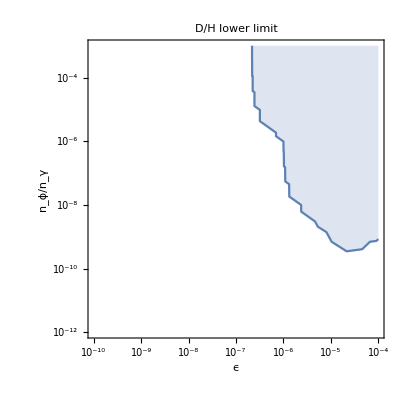

```mathematica
ListContourPlot[plotDataDoverH,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[%,Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->"D/H upper limit",PlotStyle->Orange]
ListContourPlot[plotDataDoverH,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[%,Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->"D/H lower limit"]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

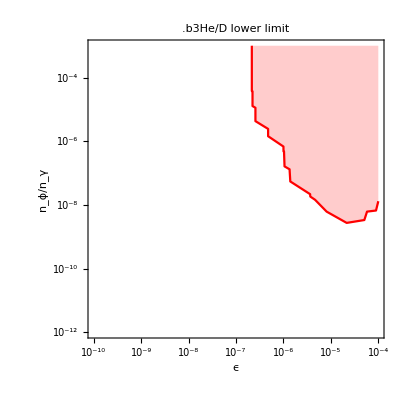

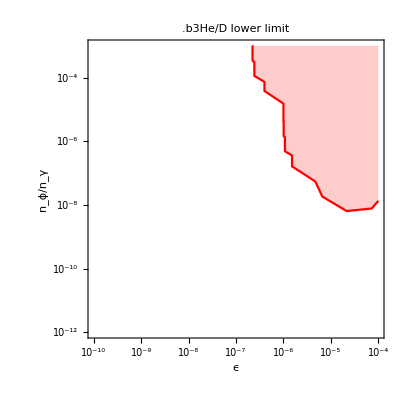

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->".b3He/D lower limit"]
```

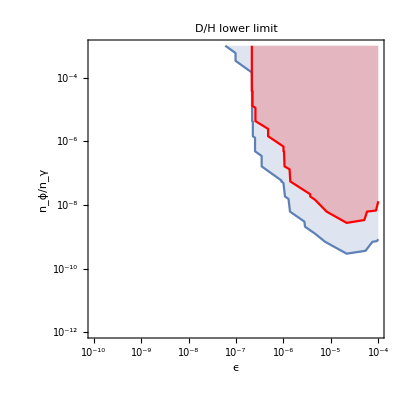

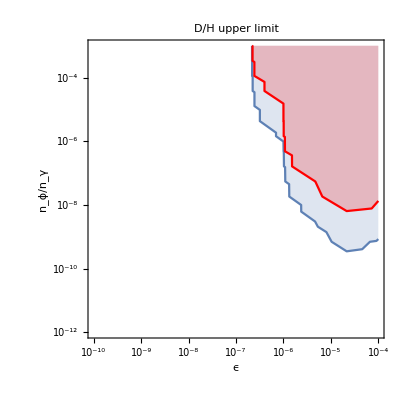

```mathematica
Show[plt2,plt3]
```